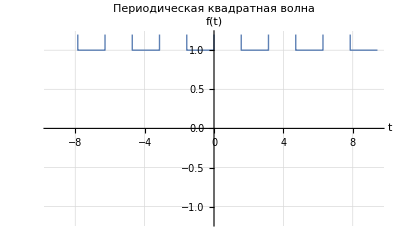

```mathematica
a=3;
b=1;
t0=0;
t1=Pi/2;
t2=Pi;
T=t2-t0;

f[t_]:=Piecewise[{{a,t0≤Mod[t,T]<t1},{b,t1≤Mod[t,T]<t2}}]

Plot[f[t],{t,-3 T,3 T},PlotStyle->Thick,AxesLabel->{"t","f(t)"},GridLines->Automatic,PlotRange->{{-3 T,3 T},{-1.2,1.2}},Exclusions->None,PlotPoints->500,PlotLabel->"Периодическая квадратная волна"]
```

A[0] = 2  B[0] = 0

A[1] = 2/π  B[1] = (1+3 Cos[12]+6 Sin[6]^2)/π

A[2] = 0  B[2] = (-1+3 Cos[12]^2+3 Sin[12]^2)/π

A[3] = -2/(3 π)  B[3] = (1+3 Cos[36]+6 Sin[18]^2)/(3 π)

A[4] = 0  B[4] = 0

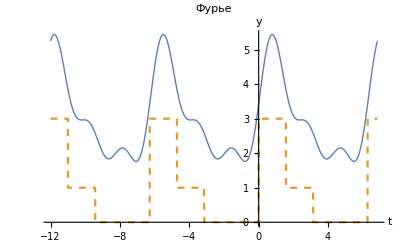

```mathematica
n=5;
h=-12;
T=2 Pi;


A[i_]:=(2/T) Integrate[f[t] Cos[(2 π i t)/T],{t,h,h+T}];
B[i_]:=(2/T) Integrate[f[t] Sin[(2 π i t)/T],{t,h,h+T}];

rad=A[0]/2;
For[i=0,i<n,i++,
Print["A[",i,"] = ",A[i],"  B[",i,"] = ",B[i]];
rad=rad+A[i] Cos[(2 π i t)/T]+B[i] Sin[(2 π i t)/T];
];

Plot[{rad,f[t]},{t,h,h+3 T},PlotStyle->{Thick,Dashed},PlotLabel->"Фурье",AxesLabel->{"t","y"},PlotRange->All,Exclusions->None]
```